# WORKSHOP 3 : STEP BARRIER POTENTIAL

Names: Quray Potosi & Angel Salazar

letf hand side: transmitted
right= transmitted and returned wave funciotn

### 1. Visualization the step potential

```mathematica
q=1;  (*height of the step potential*)
f[x_]:=Piecewise[{{-q,x<0},{q,x>0}},Indeterminate];
```

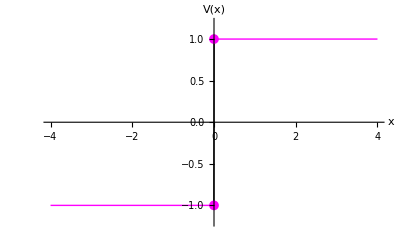

```mathematica
Plot[f[x],{x,-4,4},PlotStyle->{Thick,Magenta},AxesLabel->{"x","V(x)"},AxesOrigin->{0,0},PlotRange->{-(1.2 q),1.2 q},Exclusions->{0},ExclusionsStyle->{Thick,Black},Epilog->{AbsolutePointSize[7],Magenta,Point[{0,q}],Thick,Point[{0,-q}]  }]
```

#### Regions to the left and right of the barrier potential

The time-independent K-G Equation has different forms in the regions to the left and right of the barrier potential:

#### First region x<0:

```mathematica
sol1 = DSolve[ Subscript[ψ, 1]''[x] == -((En+a)^2-m^2) Subscript[ψ, 1][x],Subscript[ψ, 1][x],x];
TrigToExp[sol1]
```

{{ψ_1[x]→ⅇ^(√(-a^2-2 a En-En^2+m^2) x) C[1]+ⅇ^(-√(-a^2-2 a En-En^2+m^2) x) C[2]}}

Let k1 =  √((En+a)^2-m^2)

```mathematica
Subscript[ψ, 1][x_] :=c2 Exp[I k1 x] +c3 Exp[ -k1 x]
```

#### Second Region x>0

```mathematica
sol2= DSolve[ Subscript[ψ, 2]''[x] == -((En-a)^2-m^2) Subscript[ψ, 2][x],Subscript[ψ, 2][x],x];
TrigToExp[sol2]
```

{{ψ_2[x]→ⅇ^(√(-a^2+2 a En-En^2+m^2) x) C[1]+ⅇ^(-√(-a^2+2 a En-En^2+m^2) x) C[2]}}

Let k2 =  √((E-a)^2-m^2)

```mathematica
Subscript[ψ, 2][x_]:=c1 Exp[I k2 x]+ D Exp[-I k2 x] /.{D->0}
```

### 1. Defining the φ[x] equations:

```mathematica
Do[Subscript[c,i]=.,{i,3}]
Do[Subscript[ψ,i]=.,{i,2}]
Subscript[ψ, 1][x_]:=Subscript[c, 1] ⅇ^(k1 ⅈ x)+Subscript[c, 2] ⅇ^(-k1 ⅈ x)
Subscript[ψ, 2][x_]:=Subscript[c, 3] ⅇ^(ⅈ k2 x)
```

Unset::norep: Assignment on Subscript for c_1 not found.

Unset::norep: Assignment on Subscript for c_2 not found.

Unset::norep: Assignment on Subscript for c_3 not found.

General::stop: Further output of Unset::norep will be suppressed during this calculation.

Unset::norep: Assignment on Subscript for ψ_1 not found.

Unset::norep: Assignment on Subscript for ψ_2 not found.

### 3. Boundary Conditions

```mathematica
eq[1]=(Subscript[ψ, 1][x]-Subscript[ψ, 2][x]/.x->0)==0
eq[2]=(Subscript[ψ, 1]'[x]-Subscript[ψ, 2]'[x]/.x->0)==0
```

c_1+c_2-c_3==0

ⅈ k1 c_1-ⅈ k1 c_2-ⅈ k2 c_3==0

4. Getting coefficients

```mathematica
coef = Solve[{eq[1],eq[2]},{Subscript[c, 2],Subscript[c, 3]}]// FullSimplify
```

{{c_2→((k1-k2) c_1)/(k1+k2),c_3→(2 k1 c_1)/(k1+k2)}}

T can be + or - so the plot:

third region interested= supperradiance.